```mathematica
AppendTo[$Path,"/home/tohme/.julia/dev/LLROpt/mathematica-nbs"];
Get["ctmc`"]
```

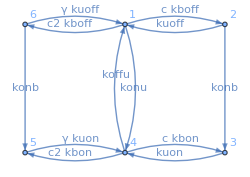

```mathematica
(*----------------------------------------------------------------------------------------------------------*)(*** Decoys, 1 binding site ***)

(*Edge lists and weights*)
edges2={{1,2},{2,1},{1,6},{6,1},{4,3},{3,4},
	    {4,5},{5,4},{6,5},{4,1},{2,3},{1,4}};
weights2={c*kboff,kuoff,c2*kboff,γ*kuoff,c*kbon,kuon,c2*kbon,γ*kuon,konb,koffu,konb,konu};
nstates2 = 6;
nedges2 = Length[edges2];
assum = c>=0&&c2>=0&&ω>=0&&γ>=0&&kboff>0&&konb>0&&kuon>0&&kbon>0&&koffu>0&&kuoff>0&&konu>0;

(*Plot the circuit*)
edgeList=Table[edges2[[i,1]]->edges2[[i,2]],{i,1,nedges2}];
g=Graph[edges2,VertexLabels->"Name",DirectedEdges->True,EdgeLabels->Table[edgeList[[i]]->Placed[(HoldForm/@weights2)[[i]],0.55],{i,1,nedges2}],ImageSize->250, GraphLayout->{"MultipartiteEmbedding","VertexPartition"->{{5,6},{4,1},{3,2}}}]
```

```mathematica
Q2 = RateMatrix[edges2, weights2, nstates2];
ss2 = SteadyStateProbabilities[Q2];
```

```mathematica
kmax =5.;
kmin=0.00001;
kdl=0.0888;
rates={c->1,c2->0,γ->10,konb->kmax,kuon->kmax, koffu->kmax,kboff->kdl,kbon->kmin,konu->kmin,kuoff->kmax};

With[{c=1.,c2=3,γ=1,kboff=1, konb=1, kuon=1, kbon=1, koffu=1, kuoff=1, konu=1},Evaluate[ss2]]
```

{0.05,0.025,0.175,0.15,0.525,0.075}

```mathematica
With[{c=1.,c2=3,γ=1,kboff=1, konb=1, kuon=1, kbon=1, koffu=1, kuoff=1, konu=1},Evaluate[]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Indeterminate

```mathematica
ClearAll[ss];
EPss[Q2]
```

Solve::ivar: {(kuon (konb+kuoff γ) (koffu konb γ+koffu kuoff γ))/(c c2 kboff kbon konb^2+c2^2 kboff kbon konb^2+c2 kboff koffu konb^2+c2 kbon konb^2 konu+«27»+koffu konb kuoff kuon γ^2+konb konu kuoff kuon γ^2+koffu kuoff^2 kuon γ^2+konu kuoff^2 kuon γ^2),«4»,(c2 kboff kuon (koffu konb γ+koffu kuoff γ))/(c c2 kboff kbon konb^2+c2^2 kboff kbon konb^2+«32»+konu kuoff^2 kuon γ^2)} is not a valid variable.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

ReplaceAll::reps: {{(-c kboff-c2 kboff-konu) ss1+koffu ss4+kuoff ss6 γ+(kuoff kuon (konb+kuoff γ) (koffu konb γ+koffu kuoff γ))/(Times[«5»]+Times[«4»]+Times[«4»]+Times[«4»]+Times[«5»]+Times[«5»]+Times[«5»]+Times[«5»]+«19»+Times[«6»]+Times[«5»]+Times[«6»]+Times[«6»]+Times[«5»]+Times[«5»]+Times[«4»]+Times[«4»]),«5»}==0,«5»,{ss1+ss3+«3»+(kuon (konb+«1») (koffu konb γ+koffu kuoff γ))/(Times[«5»]+Times[«4»]+«31»+Times[«4»]+Times[«4»]),«5»}==1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

1/2 ({Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}/.{{-((c kboff+c2 kboff+konu) ss1)+koffu ss4+kuoff ss6 γ+(koffu kuoff (konb+kuoff) kuon γ (konb+kuoff γ))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),-((c kboff+c2 kboff+konu) ss1)+koffu ss4+kuoff ss6 γ+(c kboff koffu kuoff kuon γ (konb+kuoff γ))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),-((c kboff+c2 kboff+konu) ss1)+koffu ss4+kuoff ss6 γ+(c kuoff γ (c2 kboff kbon konb (konb+kuoff)+c kboff kbon konb (konb+kuoff γ)+(kboff koffu konb+kbon konu (konb+kuoff)) (konb+kuoff γ)))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),-((c kboff+c2 kboff+konu) ss1)+koffu ss4+kuoff ss6 γ+(kuoff kuon γ (c kboff konb (konb+kuoff γ)+(konb+kuoff) (c2 kboff konb+konu (konb+kuoff γ))))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),-((c kboff+c2 kboff+konu) ss1)+koffu ss4+kuoff ss6 γ+(c2 kuoff (c kboff kbon konb (konb+kuoff γ)+(konb+kuoff) (c2 kboff kbon konb+kboff koffu konb+kbon konu (konb+kuoff γ))))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),-((c kboff+c2 kboff+konu) ss1)+koffu ss4+kuoff ss6 γ+(c2 kboff koffu kuoff (konb+kuoff) kuon γ)/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ))))}==0,{c kboff ss1-(koffu (konb+kuoff)^2 kuon γ (konb+kuoff γ))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),c kboff (ss1-(koffu (konb+kuoff) kuon γ (konb+kuoff γ))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ))))),c kboff ss1-(c (konb+kuoff) γ (c2 kboff kbon konb (konb+kuoff)+c kboff kbon konb (konb+kuoff γ)+(kboff koffu konb+kbon konu (konb+kuoff)) (konb+kuoff γ)))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),c kboff ss1-((konb+kuoff) kuon γ (c kboff konb (konb+kuoff γ)+(konb+kuoff) (c2 kboff konb+konu (konb+kuoff γ))))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),c kboff ss1-(c2 (konb+kuoff) (c kboff kbon konb (konb+kuoff γ)+(konb+kuoff) (c2 kboff kbon konb+kboff koffu konb+kbon konu (konb+kuoff γ))))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),c kboff ss1-(c2 kboff koffu (konb+kuoff)^2 kuon γ)/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ))))}==0,{-kuon ss3+c kbon ss4+(koffu konb (konb+kuoff) kuon γ (konb+kuoff γ))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),-kuon ss3+c kbon ss4+(c kboff koffu konb kuon γ (konb+kuoff γ))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),-kuon ss3+c kbon ss4+(c konb γ (c2 kboff kbon konb (konb+kuoff)+c kboff kbon konb (konb+kuoff γ)+(kboff koffu konb+kbon konu (konb+kuoff)) (konb+kuoff γ)))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),-kuon ss3+c kbon ss4+(konb kuon γ (c kboff konb (konb+kuoff γ)+(konb+kuoff) (c2 kboff konb+konu (konb+kuoff γ))))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),-kuon ss3+c kbon ss4+(c2 konb (c kboff kbon konb (konb+kuoff γ)+(konb+kuoff) (c2 kboff kbon konb+kboff koffu konb+kbon konu (konb+kuoff γ))))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),-kuon ss3+c kbon ss4+(c2 kboff koffu konb (konb+kuoff) kuon γ)/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ))))}==0,{konu ss1-(c kbon+c2 kbon+koffu) ss4+kuon (ss3+ss5 γ),konu ss1-(c kbon+c2 kbon+koffu) ss4+kuon (ss3+ss5 γ),konu ss1-(c kbon+c2 kbon+koffu) ss4+kuon (ss3+ss5 γ),konu ss1-(c kbon+c2 kbon+koffu) ss4+kuon (ss3+ss5 γ),konu ss1-(c kbon+c2 kbon+koffu) ss4+kuon (ss3+ss5 γ),konu ss1-(c kbon+c2 kbon+koffu) ss4+kuon (ss3+ss5 γ)}==0,{c2 kbon ss4+konb ss6-kuon ss5 γ,c2 kbon ss4+konb ss6-kuon ss5 γ,c2 kbon ss4+konb ss6-kuon ss5 γ,c2 kbon ss4+konb ss6-kuon ss5 γ,c2 kbon ss4+konb ss6-kuon ss5 γ,c2 kbon ss4+konb ss6-kuon ss5 γ}==0,{c2 kboff ss1-ss6 (konb+kuoff γ),c2 kboff ss1-ss6 (konb+kuoff γ),c2 kboff ss1-ss6 (konb+kuoff γ),c2 kboff ss1-ss6 (konb+kuoff γ),c2 kboff ss1-ss6 (konb+kuoff γ),c2 kboff ss1-ss6 (konb+kuoff γ)}==0,{ss1+ss3+ss4+ss5+ss6+(koffu (konb+kuoff) kuon γ (konb+kuoff γ))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),ss1+ss3+ss4+ss5+ss6+(c kboff koffu kuon γ (konb+kuoff γ))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),ss1+ss3+ss4+ss5+ss6+(c γ (c2 kboff kbon konb (konb+kuoff)+c kboff kbon konb (konb+kuoff γ)+(kboff koffu konb+kbon konu (konb+kuoff)) (konb+kuoff γ)))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),ss1+ss3+ss4+ss5+ss6+(kuon γ (c kboff konb (konb+kuoff γ)+(konb+kuoff) (c2 kboff konb+konu (konb+kuoff γ))))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),ss1+ss3+ss4+ss5+ss6+(c2 (c kboff kbon konb (konb+kuoff γ)+(konb+kuoff) (c2 kboff kbon konb+kboff koffu konb+kbon konu (konb+kuoff γ))))/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ)))),ss1+ss3+ss4+ss5+ss6+(c2 kboff koffu (konb+kuoff) kuon γ)/(c^2 kboff kbon konb γ (konb+kuoff γ)+c ((kbon konu (konb+kuoff)+kboff konb kuon+kboff koffu (konb+kuon)) γ (konb+kuoff γ)+c2 kboff kbon konb (konb+konb γ+2 kuoff γ))+(konb+kuoff) (c2^2 kboff kbon konb+c2 kbon konu (konb+kuoff γ)+(koffu+konu) kuon γ (konb+kuoff γ)+c2 kboff (konb kuon γ+koffu (konb+kuon γ))))}==1})